## Spectral Decomposition

### References

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Topological_space"]
```

Topological space

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Vector_space"]
```

Vector space

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Metric_space"]
```

Metric space

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Norm_%28mathematics%29"]
```

Norm

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Banach_space"]
```

Banach space

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Hilbert_space"]
```

Hilbert space

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Hermitian_adjoint"]
```

Adjoint

WolframAlphaQueryResults

```mathematica
Hyperlink["http://en.wikipedia.org/wiki/Transfer_operator"]
Hyperlink["http://en.wikipedia.org/wiki/Composition_operator"]
```

Perron-Frobenius operator

WolframAlphaQueryResults

Composition operator

WolframAlphaQueryResults

### Initialization

```mathematica
M := {{1,1},{1,2}}
𝔉[{x_,y_}] := M.{x,y}
F[{x_,y_}]:= Mod[𝔉[{x,y}],1]
```

```mathematica
invM:=Inverse[M]
inv𝔉[{x_,y_}]:=invM.{x,y}
invF[{x_,y_}] := Mod[inv𝔉[{x,y}],1]
```

```mathematica
invFF[{x_,y_}] := Piecewise[{{invM.{x,y}-{-1,0},2x ≤ y},{invM.{x,y},x≤ y<2x},{invM.{x,y}-{0,-1},2x-1≤ y < x},{invM.{x,y}-{1,-1},y<2x-1 }}]
```

```mathematica
σDef:=σ->(3+Sqrt[5])/2
ϕDef:= ϕ->(1+Sqrt[5])/2
```

### Definitions

The Ruelle-Perron-Frobenius operator (Transfer operator) of the Arnold cat map. The Eulerian point of view: follow the evolution of a measure at a given point.

```mathematica
ℒ[ρ_,{x_,y_}] := ρ[invF[{x,y}]]
```

The Koopman operator (Composition operator) of the Arnold cat map. The Lagrangian point of view: follow the value of a measure along an orbit.

```mathematica
𝔎[ρ_,{x_,y_}] := ρ[F[{x,y}]]
```

### The space of smooth distributions

The effect of the Transfer operator is stretching a distribution along the unstable manifold and compressing and folding it along the stable manifold.

```mathematica
um={Thick,Red,Line[{{0,0},{1,ϕ/.ϕDef//N}}]};
```

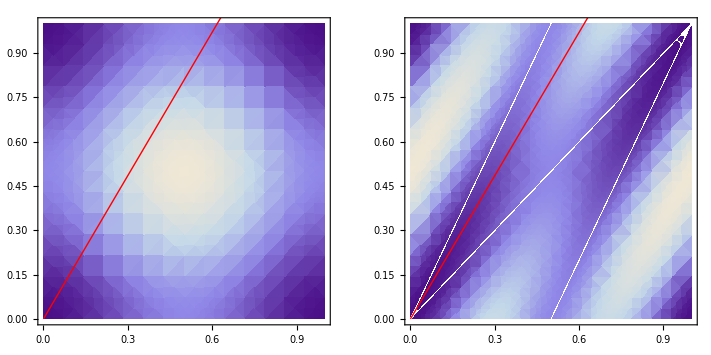

```mathematica
GraphicsGrid[{{Show[DensityPlot[(Sin[Pi x]^2+1)(Sin[Pi y]^2+1)/4,{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],
Show[DensityPlot[(Sin[Pi invF[{x,y}][[1]]]^2+1)(Sin[Pi invF[{x,y}][[2]]]^2+1)/4,{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]}}]
```

```mathematica
Plot3D[(Sin[Pi x]^2+1)(Sin[Pi y]^2+1)/4,{x,0,1},{y,0,1},MaxRecursion->0,AspectRatio->Automatic,ImageSize->Scaled[0.5],Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]
Plot3D[(Sin[Pi invF[{x,y}][[1]]]^2+1)(Sin[Pi invF[{x,y}][[2]]]^2+1)/4,{x,0,1},{y,0,1},MaxRecursion->2,AspectRatio->Automatic,ImageSize->Scaled[0.5],Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]
Plot3D[(Sin[Pi invF[invF[{x,y}]][[1]]]^2+1)(Sin[Pi invF[invF[{x,y}]][[2]]]^2+1)/4,{x,0,1},{y,0,1},MaxRecursion->4,AspectRatio->Automatic,ImageSize->Scaled[0.5],Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]
Plot3D[(Sin[Pi invF[invF[invF[{x,y}]]][[1]]]^2+1)(Sin[Pi invF[invF[invF[{x,y}]]][[2]]]^2+1)/4,{x,0,1},{y,0,1},MaxRecursion->6,AspectRatio->Automatic,ImageSize->Scaled[0.5],Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
ψ[{k_Integer,l_Integer},{x_,y_}]:=Exp[-2 Pi I(k x+l y)]
```

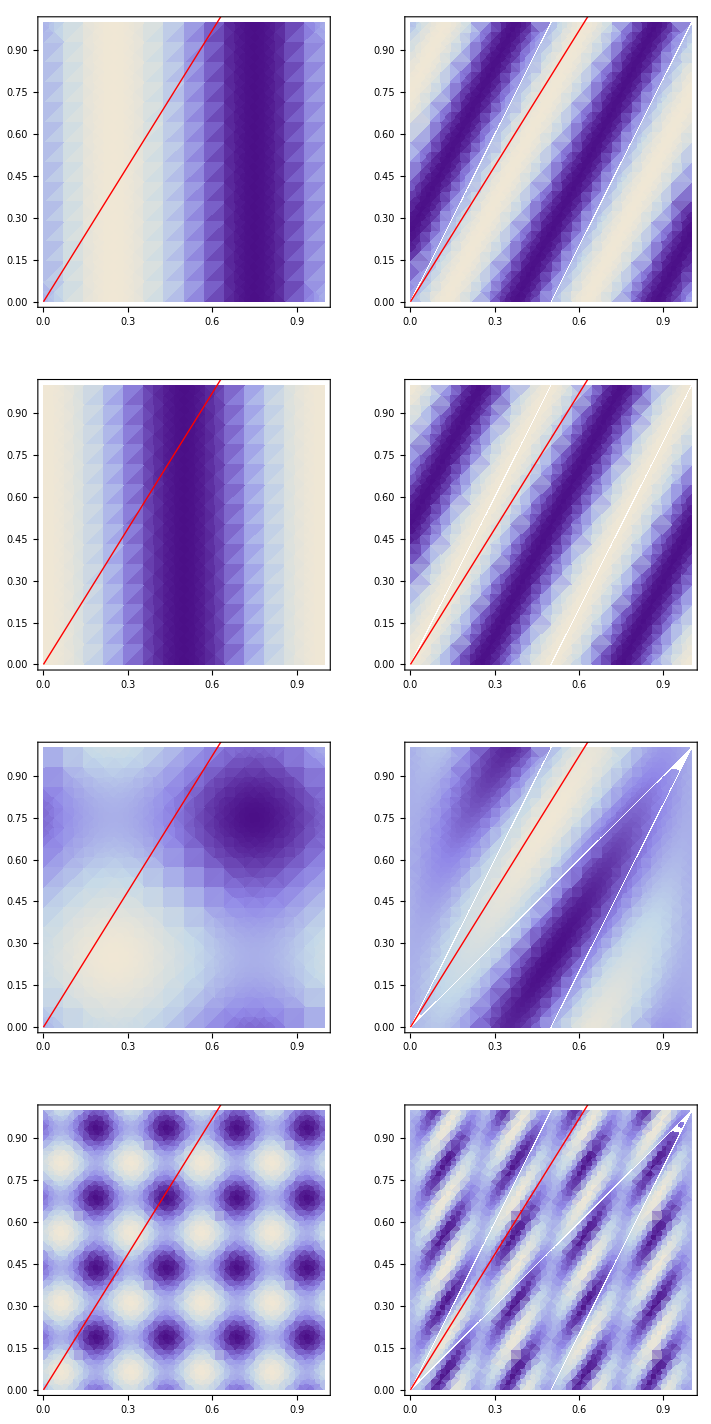

```mathematica
GraphicsGrid[{{Show[DensityPlot[Sin[2 Pi x],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Sin[2 Pi invF[{x,y}][[1]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]},
{Show[DensityPlot[Cos[2 Pi x],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Cos[2 Pi invF[{x,y}][[1]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]},
{Show[DensityPlot[Sin[2 Pi x]+Sin[2 Pi y],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Sin[2 Pi invF[{x,y}][[1]]]+Sin[2 Pi invF[{x,y}][[2]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]},
{Show[DensityPlot[Sin[8 Pi x]+Sin[8 Pi y],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Sin[8 Pi invF[{x,y}][[1]]]+Sin[8 Pi invF[{x,y}][[2]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]}}]
```

```mathematica
inv𝔉[{x,y}]
{Subscript[k, x],Subscript[k, y]}.inv𝔉[{x,y}]
{Subscript[k, x],Subscript[k, y]}.invM
invM.{Subscript[k, x],Subscript[k, y]}
```

{2 x-y,-x+y}

(2 x-y) k_x+(-x+y) k_y

{2 k_x-k_y,-k_x+k_y}

{2 k_x-k_y,-k_x+k_y}

The cat map in Fourier space.

```mathematica
FK[{kx_,ky_}]:= {kx,ky}.invM
FK[{Subscript[k, x],Subscript[k, y]}]
```

{2 k_x-k_y,-k_x+k_y}

Iterating the map in Fourier space sends any wave vector (k,l) to vectors such that l/k tends asymptotically to -1/ϕ with ever increasing wave number (fixed point on the projective line).

```mathematica
Nest[FK,{k,l},10]//Simplify
%[[2]]/%[[1]]
```

{10946 k-6765 l,-6765 k+4181 l}

(-6765 k+4181 l)/(10946 k-6765 l)

```mathematica
Nest[FK,{1,0},10]//Simplify
%[[2]]/%[[1]]//N
Nest[FK,{2,1},10]//Simplify
%[[2]]/%[[1]]//N
Nest[FK,{0,-1},10]//Simplify
%[[2]]/%[[1]]//N
-1/ϕ/.ϕDef//N
```

{10946,-6765}

-0.618034

{15127,-9349}

-0.618034

{6765,-4181}

-0.618034

-0.618034

The effect is to damp the dependency of a distribution on the coordinate along the unstable manifold which is orthogonal to  l/k=-1/ϕ.

```mathematica
X={x,y}
```

{x,y}

{1,0}

{2,-1}

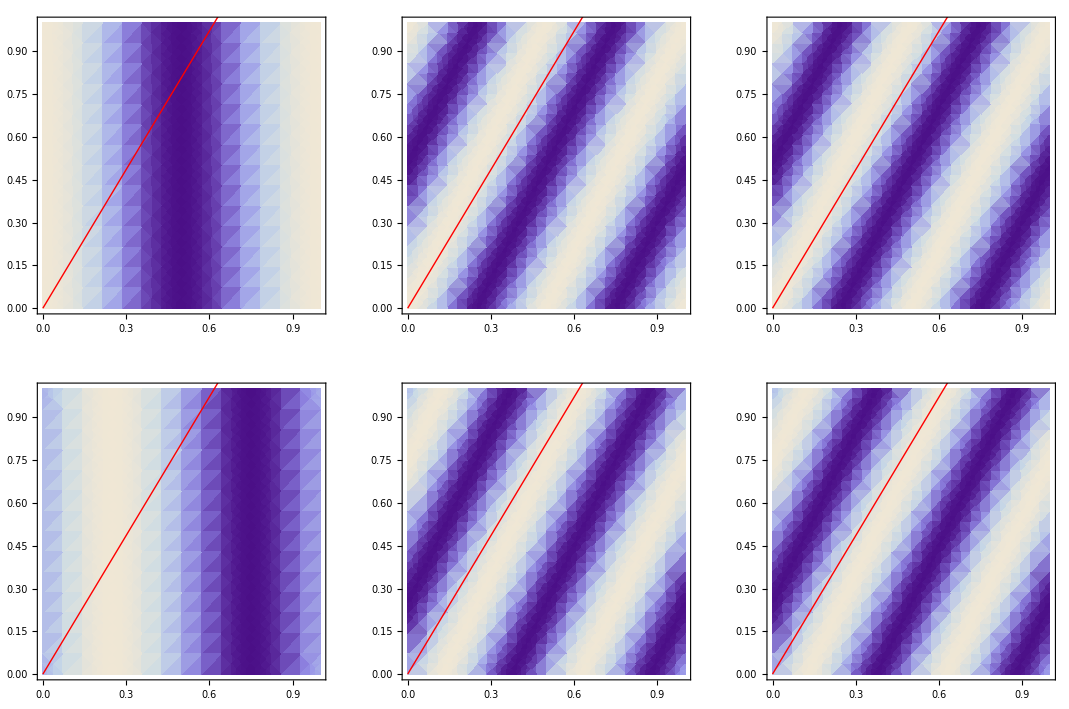

```mathematica
K={1,0}
KK=FK[K]
GraphicsGrid[{{Show[DensityPlot[Re[Exp[2Pi I K.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Re[Exp[2Pi I K.invFF[X]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Re[Exp[2Pi I KK.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]},
{Show[DensityPlot[Im[Exp[2Pi I K.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Im[Exp[2Pi I K.invFF[X]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Im[Exp[2Pi I KK.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]}}]
```

{0,1}

{-1,1}

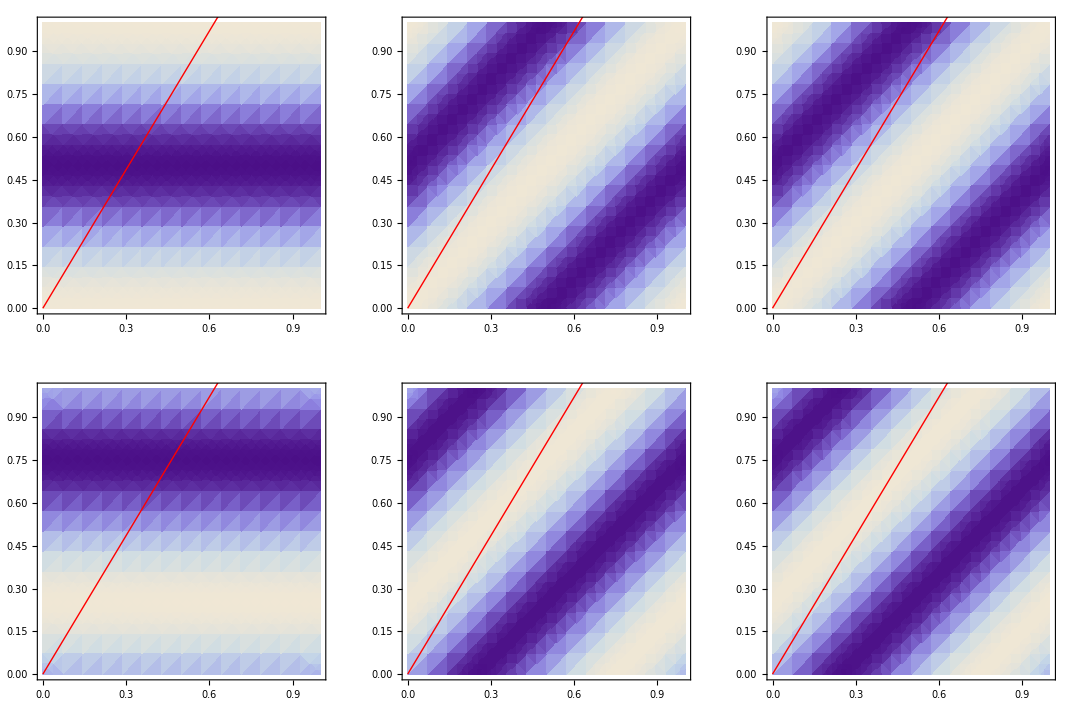

```mathematica
K={0,1}
KK=FK[K]
GraphicsGrid[{{Show[DensityPlot[Re[Exp[2Pi I K.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Re[Exp[2Pi I K.invFF[X]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Re[Exp[2Pi I KK.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]},
{Show[DensityPlot[Im[Exp[2Pi I K.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Im[Exp[2Pi I K.invFF[X]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Im[Exp[2Pi I KK.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]}}]
```

{-3,2}

{-8,5}

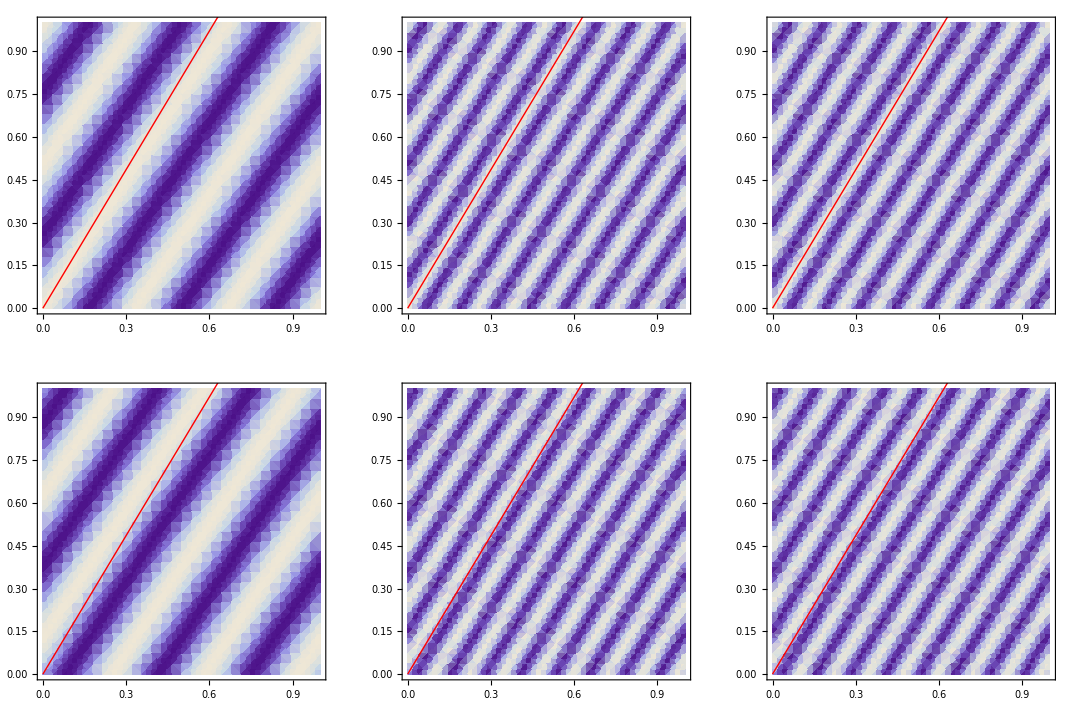

```mathematica
K={-3,2}
KK=FK[K]
GraphicsGrid[{{Show[DensityPlot[Re[Exp[2Pi I K.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Re[Exp[2Pi I K.invFF[X]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Re[Exp[2Pi I KK.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]},
{Show[DensityPlot[Im[Exp[2Pi I K.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Im[Exp[2Pi I K.invFF[X]]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]],Show[DensityPlot[Im[Exp[2Pi I KK.X]],{x,0,1},{y,0,1},AspectRatio->Automatic,ImageSize->Scaled[0.75]],Graphics[um]]}}]
```

```mathematica
index[n_,{k_,l_}] := k (2n-1) + l
Kindex[n_,i_]:={IntegerPart[i/(2n-1)],i-IntegerPart[i/(2n-1)](2n-1)}
```

```mathematica
n=3
Table[{k,l},{k,-n+1,n-1},{l,-n+1,n-1}]//TraditionalForm
index[n,#]&/@Flatten[%,1]
Partition[%,2n-1]//TraditionalForm
Map[Kindex[n,#]&,%,{2}]//TraditionalForm
```

3

({-2,-2} | {-2,-1} | {-2,0} | {-2,1} | {-2,2}
{-1,-2} | {-1,-1} | {-1,0} | {-1,1} | {-1,2}
{0,-2} | {0,-1} | {0,0} | {0,1} | {0,2}
{1,-2} | {1,-1} | {1,0} | {1,1} | {1,2}
{2,-2} | {2,-1} | {2,0} | {2,1} | {2,2})

{-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12}

(-12 | -11 | -10 | -9 | -8
-7 | -6 | -5 | -4 | -3
-2 | -1 | 0 | 1 | 2
3 | 4 | 5 | 6 | 7
8 | 9 | 10 | 11 | 12)

({-2,-2} | {-2,-1} | {-2,0} | {-1,-4} | {-1,-3}
{-1,-2} | {-1,-1} | {-1,0} | {0,-4} | {0,-3}
{0,-2} | {0,-1} | {0,0} | {0,1} | {0,2}
{0,3} | {0,4} | {1,0} | {1,1} | {1,2}
{1,3} | {1,4} | {2,0} | {2,1} | {2,2})

```mathematica
mi[n_,i_]:=IntegerPart[(i+Sign[i](n-1))/(2*n-1)]
Fi[n_,i_]:=-2(n-1)(i-mi[n,i](2n-1))+mi[n,i](4n-3)
```

```mathematica
Table[i,{i,-22,+22}]
{#,mi[3,#]}&/@%
```

{-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

{{-22,-4},{-21,-4},{-20,-4},{-19,-4},{-18,-4},{-17,-3},{-16,-3},{-15,-3},{-14,-3},{-13,-3},{-12,-2},{-11,-2},{-10,-2},{-9,-2},{-8,-2},{-7,-1},{-6,-1},{-5,-1},{-4,-1},{-3,-1},{-2,0},{-1,0},{0,0},{1,0},{2,0},{3,1},{4,1},{5,1},{6,1},{7,1},{8,2},{9,2},{10,2},{11,2},{12,2},{13,3},{14,3},{15,3},{16,3},{17,3},{18,4},{19,4},{20,4},{21,4},{22,4}}

#### n=3

```mathematica
n=3
nn=2n(n-1)
2 nn+1
```

3

12

25

{-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12}

{{-12,-10},{-11,-14},{-10,-18},{-9,-22},{-8,-26},{-7,-1},{-6,-5},{-5,-9},{-4,-13},{-3,-17},{-2,8},{-1,4},{0,0},{1,-4},{2,-8},{3,17},{4,13},{5,9},{6,5},{7,1},{8,26},{9,22},{10,18},{11,14},{12,10}}

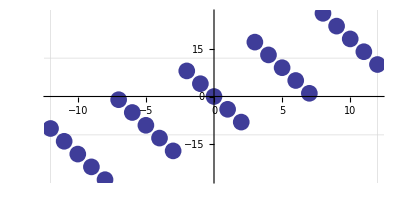

```mathematica
Table[i,{i,-nn,+nn}]
{#,Fi[n,#]}&/@%
ListPlot[%,AspectRatio->0.5,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.03],GridLines->{{-nn,0,nn},{-nn,0,nn}}]
```

```mathematica
sparseL = {};
Do[
If[j-nn== Fi[n,i-nn],AppendTo[sparseL,{i+1,j+1}-> 1]],
{i,0,2nn+1},{j,0,2nn+1}]
sparseL
L=SparseArray[sparseL];
ArrayPlot[Normal[L],Mesh->True]
```

{{1,3}→1,{6,12}→1,{7,8}→1,{8,4}→1,{11,21}→1,{12,17}→1,{13,13}→1,{14,9}→1,{15,5}→1,{17,26}→1,{18,22}→1,{19,18}→1,{20,14}→1,{25,23}→1}

-Graphics-

#### n=5

```mathematica
n=5
nn=2n(n-1)
2 nn+1
```

5

40

81

{-40,-39,-38,-37,-36,-35,-34,-33,-32,-31,-30,-29,-28,-27,-26,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

{{-40,-36},{-39,-44},{-38,-52},{-37,-60},{-36,-68},{-35,-76},{-34,-84},{-33,-92},{-32,-100},{-31,-19},{-30,-27},{-29,-35},{-28,-43},{-27,-51},{-26,-59},{-25,-67},{-24,-75},{-23,-83},{-22,-2},{-21,-10},{-20,-18},{-19,-26},{-18,-34},{-17,-42},{-16,-50},{-15,-58},{-14,-66},{-13,15},{-12,7},{-11,-1},{-10,-9},{-9,-17},{-8,-25},{-7,-33},{-6,-41},{-5,-49},{-4,32},{-3,24},{-2,16},{-1,8},{0,0},{1,-8},{2,-16},{3,-24},{4,-32},{5,49},{6,41},{7,33},{8,25},{9,17},{10,9},{11,1},{12,-7},{13,-15},{14,66},{15,58},{16,50},{17,42},{18,34},{19,26},{20,18},{21,10},{22,2},{23,83},{24,75},{25,67},{26,59},{27,51},{28,43},{29,35},{30,27},{31,19},{32,100},{33,92},{34,84},{35,76},{36,68},{37,60},{38,52},{39,44},{40,36}}

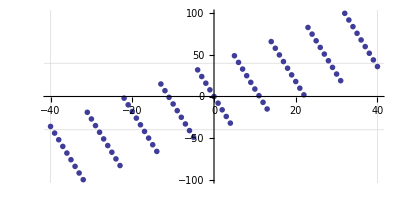

```mathematica
Table[i,{i,-nn,+nn}]
{#,Fi[n,#]}&/@%
ListPlot[%,AspectRatio->0.5,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.01],GridLines->{{-nn,0,nn},{-nn,0,nn}}]
```

```mathematica
sparseL = {};
Do[
If[j-nn== Fi[n,i-nn],AppendTo[sparseL,{i+1,j+1}-> 1]],
{i,0,2nn+1},{j,0,2nn+1}]
sparseL
L=SparseArray[sparseL];
ArrayPlot[Normal[L],Mesh->True]
```

{{1,5}→1,{10,22}→1,{11,14}→1,{12,6}→1,{19,39}→1,{20,31}→1,{21,23}→1,{22,15}→1,{23,7}→1,{28,56}→1,{29,48}→1,{30,40}→1,{31,32}→1,{32,24}→1,{33,16}→1,{34,8}→1,{37,73}→1,{38,65}→1,{39,57}→1,{40,49}→1,{41,41}→1,{42,33}→1,{43,25}→1,{44,17}→1,{45,9}→1,{47,82}→1,{48,74}→1,{49,66}→1,{50,58}→1,{51,50}→1,{52,42}→1,{53,34}→1,{54,26}→1,{59,75}→1,{60,67}→1,{61,59}→1,{62,51}→1,{63,43}→1,{70,76}→1,{71,68}→1,{72,60}→1,{81,77}→1}

-Graphics-

#### n=7

```mathematica
n=7
nn=2n(n-1)
2 nn+1
```

7

84

169

{-84,-83,-82,-81,-80,-79,-78,-77,-76,-75,-74,-73,-72,-71,-70,-69,-68,-67,-66,-65,-64,-63,-62,-61,-60,-59,-58,-57,-56,-55,-54,-53,-52,-51,-50,-49,-48,-47,-46,-45,-44,-43,-42,-41,-40,-39,-38,-37,-36,-35,-34,-33,-32,-31,-30,-29,-28,-27,-26,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84}

{{-84,-78},{-83,-90},{-82,-102},{-81,-114},{-80,-126},{-79,-138},{-78,-150},{-77,-162},{-76,-174},{-75,-186},{-74,-198},{-73,-210},{-72,-222},{-71,-53},{-70,-65},{-69,-77},{-68,-89},{-67,-101},{-66,-113},{-65,-125},{-64,-137},{-63,-149},{-62,-161},{-61,-173},{-60,-185},{-59,-197},{-58,-28},{-57,-40},{-56,-52},{-55,-64},{-54,-76},{-53,-88},{-52,-100},{-51,-112},{-50,-124},{-49,-136},{-48,-148},{-47,-160},{-46,-172},{-45,-3},{-44,-15},{-43,-27},{-42,-39},{-41,-51},{-40,-63},{-39,-75},{-38,-87},{-37,-99},{-36,-111},{-35,-123},{-34,-135},{-33,-147},{-32,22},{-31,10},{-30,-2},{-29,-14},{-28,-26},{-27,-38},{-26,-50},{-25,-62},{-24,-74},{-23,-86},{-22,-98},{-21,-110},{-20,-122},{-19,47},{-18,35},{-17,23},{-16,11},{-15,-1},{-14,-13},{-13,-25},{-12,-37},{-11,-49},{-10,-61},{-9,-73},{-8,-85},{-7,-97},{-6,72},{-5,60},{-4,48},{-3,36},{-2,24},{-1,12},{0,0},{1,-12},{2,-24},{3,-36},{4,-48},{5,-60},{6,-72},{7,97},{8,85},{9,73},{10,61},{11,49},{12,37},{13,25},{14,13},{15,1},{16,-11},{17,-23},{18,-35},{19,-47},{20,122},{21,110},{22,98},{23,86},{24,74},{25,62},{26,50},{27,38},{28,26},{29,14},{30,2},{31,-10},{32,-22},{33,147},{34,135},{35,123},{36,111},{37,99},{38,87},{39,75},{40,63},{41,51},{42,39},{43,27},{44,15},{45,3},{46,172},{47,160},{48,148},{49,136},{50,124},{51,112},{52,100},{53,88},{54,76},{55,64},{56,52},{57,40},{58,28},{59,197},{60,185},{61,173},{62,161},{63,149},{64,137},{65,125},{66,113},{67,101},{68,89},{69,77},{70,65},{71,53},{72,222},{73,210},{74,198},{75,186},{76,174},{77,162},{78,150},{79,138},{80,126},{81,114},{82,102},{83,90},{84,78}}

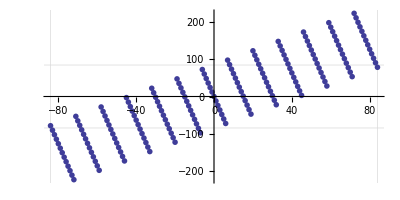

```mathematica
Table[i,{i,-nn,+nn}]
{#,Fi[n,#]}&/@%
ListPlot[%,AspectRatio->0.5,ImageSize->Scaled[0.5],PlotStyle->PointSize[0.01],GridLines->{{-nn,0,nn},{-nn,0,nn}}]
```

```mathematica
sparseL = {};
Do[
If[j-nn== Fi[n,i-nn],AppendTo[sparseL,{i+1,j+1}-> 1]],
{i,0,2nn+1},{j,0,2nn+1}]
sparseL
L=SparseArray[sparseL];
ArrayPlot[Normal[L],Mesh->True]
```

{{1,7}→1,{14,32}→1,{15,20}→1,{16,8}→1,{27,57}→1,{28,45}→1,{29,33}→1,{30,21}→1,{31,9}→1,{40,82}→1,{41,70}→1,{42,58}→1,{43,46}→1,{44,34}→1,{45,22}→1,{46,10}→1,{53,107}→1,{54,95}→1,{55,83}→1,{56,71}→1,{57,59}→1,{58,47}→1,{59,35}→1,{60,23}→1,{61,11}→1,{66,132}→1,{67,120}→1,{68,108}→1,{69,96}→1,{70,84}→1,{71,72}→1,{72,60}→1,{73,48}→1,{74,36}→1,{75,24}→1,{76,12}→1,{79,157}→1,{80,145}→1,{81,133}→1,{82,121}→1,{83,109}→1,{84,97}→1,{85,85}→1,{86,73}→1,{87,61}→1,{88,49}→1,{89,37}→1,{90,25}→1,{91,13}→1,{93,170}→1,{94,158}→1,{95,146}→1,{96,134}→1,{97,122}→1,{98,110}→1,{99,98}→1,{100,86}→1,{101,74}→1,{102,62}→1,{103,50}→1,{104,38}→1,{109,159}→1,{110,147}→1,{111,135}→1,{112,123}→1,{113,111}→1,{114,99}→1,{115,87}→1,{116,75}→1,{117,63}→1,{124,160}→1,{125,148}→1,{126,136}→1,{127,124}→1,{128,112}→1,{129,100}→1,{130,88}→1,{139,161}→1,{140,149}→1,{141,137}→1,{142,125}→1,{143,113}→1,{154,162}→1,{155,150}→1,{156,138}→1,{169,163}→1}

-Graphics-